```mathematica
Print@Names["paul`*"]
```

```mathematica
Graphics3D[{ImportObjVC@"rgb triangle.obj"},Lighting->{{"Ambient",White}}]
Graphics3D[{EdgeForm[None],ImportObjVC@"sokrates.obj"},Lighting->{{"Ambient",White}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*pointing outwards in 2d note that the color along a given line from the center is constant*)
(*2D normal maps are enough to reconstruct 3D normals, c.f. formula for unit sphere normal map*)
ListNormalVectorPlot@Transpose@CoordinateBoundsArray[Table[{-1,1},2],0.01]

(*pointing to {x,y,1}. Now there is much more blue*)
ListNormalVectorPlot@Map[#~Append~1&,Transpose@CoordinateBoundsArray[Table[{-1,1},2],0.01],{2}]

(*unit sphere normal map, c.f. https://www.filterforge.com/filters/6487-normal.html *)
(*note: the colors at the outline correspond to that in the first picture*)
<<numerics`
ListNormalVectorPlot@Map[
If[1-Norm2@#<0
,{0,0,0}1.
,#~Append~Sqrt[1-Norm2@#](*extend to unit normal/point on unit sphere*)
]&,

Transpose@CoordinateBoundsArray[Table[{-1,1},2],0.005],

{2}
]
```

-Graphics-

-Graphics-

-Graphics-

{{0.621256,0.382281,-0.0485134,0.757376,0.591709,-0.0479351,-0.213449,-0.344703,0.62098,0.504475},{0.486827,0.924124,-0.655096,0.0548844,0.423053,0.186515,-0.63956,-0.185881,0.342784,0.706804},{0.0537286,-0.234407,-0.0668476,0.51005,0.556852,-0.919359,-0.332206,0.54001,0.0221519,0.191673},{-0.202167,-0.448763,0.366911,0.350453,-0.353576,-0.963106,-0.931426,-0.455872,-0.678936,-0.9032}}

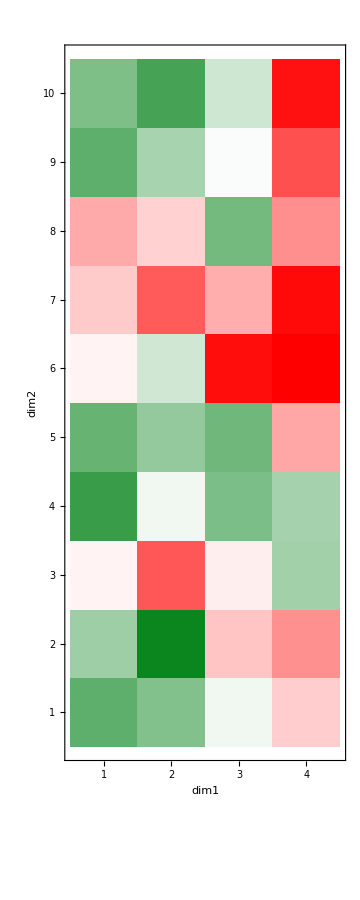
-Graphics-MatrixPlot

{Speed,Quality}

```mathematica
m=RandomReal[{-1,1},{4,10}]
ShowDistanceField[m,Method->MatrixPlot]~Labeled~MatrixPlot
Labeled[ShowDistanceField[m,PerformanceGoal->#],#]&/@{"Speed","Quality"}
```

```mathematica
(*demo*)
m=Table[
Sin[3.x]Sin[3.y]Sin[3.z]-0.5
,{x,0.,3.,0.1},{y,0.,3.,0.1},{z,-1.,1.,0.1}];
m=Table[x-5,{x,10},{y,4},{z,6}](**)(*dim1,dim2,dim3*);
m=RandomReal[{-1,1},{10,4,6}];
$PrePrint=.;
{ShowDistanceField3DSlice[m,Method->MatrixPlot]~Labeled~ShowDistanceField3DSlice[MatrixPlot]}~Join~
(ShowDistanceField3DSlice[m,PerformanceGoal->#]~Labeled~ShowDistanceField3DSlice[#]&/@{"Speed","Quality"})

{ShowDistanceField3D[m,Method->Image3D]~Labeled~Image3D}~Join~(ShowDistanceField3D[m,PerformanceGoal->#]~Labeled~#&/@{"Speed","Quality"(*,"HighQuality"*)})
```

{ShowDistanceField3DSlice[MatrixPlot],ShowDistanceField3DSlice[Speed],ShowDistanceField3DSlice[Quality]}

{-Graphics3D-Image3D,Speed,Quality}